```mathematica
Exit
```

```mathematica
(*Delete all compiled dynamic libraries of the CycleSamplerLink package.*)
If[
FileExistsQ[#],DeleteDirectory[#,DeleteContents->True]
]&[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"LibraryResources",$SystemID}]]
```

```mathematica
Get[
FileNameJoin[{ParentDirectory[NotebookDirectory[]],"CycleSamplerLink.m"}]
]
```

```mathematica
d=3;
n=16;
r=ConstantArray[1.,n];
p=2;
samplecount=1000000;
moments=Table[
Sum[
Block[{a,mean},
a=RandomClosedPolygons[3,r,samplecount];

mean=Mean[a["EdgeQuotientSpaceSamplingWeights"]^p]
]
,{k}
]/k,
{k,{1,2,4,8,16,32,64,128,256}}]
```

{2.30746×10^-6,2.29541×10^-6,2.31145×10^-6,2.2969×10^-6,2.31179×10^-6,2.31334×10^-6,2.31635×10^-6,2.3136×10^-6,2.31058×10^-6}

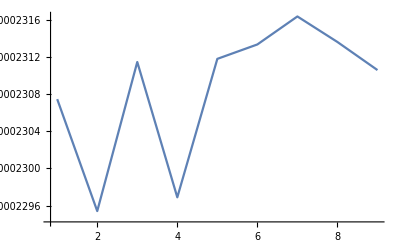

```mathematica
ListLinePlot[moments,PlotRange->All]
```

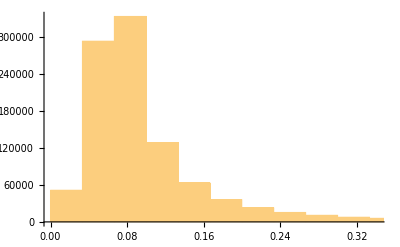

```mathematica
Histogram[a["EdgeQuotientSpaceSamplingWeights"]]
```

```mathematica
a//Keys
```

{OpenPolygonUnitEdgeVectors,ShiftVectors,ClosedPolygonUnitEdgeVectors,EdgeSpaceSamplingWeights,EdgeQuotientSpaceSamplingWeights,EdgeLengths,SphereRadii}

0.113311

```mathematica
data1=CycleSampleChordLength[d,r,{1,3},samplecount,"QuotientSpace"->False];//AbsoluteTiming//First
data2=CycleSampleChordLength[d,r,{1,3},samplecount,"QuotientSpace"->True];//AbsoluteTiming//First
Histogram[{data1,data2},"Wand","CDF",PlotRange->All]
```

```mathematica
n=40;
a=RandomClosedPolygons[3,ConstantArray[1.,n],1000000];//AbsoluteTiming
b=ActionAngleSample[n,1000000];//AbsoluteTiming
a=RandomClosedPolygons[3,ConstantArray[1.,n],1000000];//AbsoluteTiming
b=ActionAngleSample[n,1000000];//AbsoluteTiming
```

```mathematica
n=32;
a=RandomClosedPolygons[3,ConstantArray[1.,n],1000000];//AbsoluteTiming
b=ActionAngleSample[n,1000000];//AbsoluteTiming
a=RandomClosedPolygons[3,ConstantArray[1.,n],1000000];//AbsoluteTiming
b=ActionAngleSample[n,1000000];//AbsoluteTiming
```

```mathematica
n=28;
a=RandomClosedPolygons[3,ConstantArray[1.,n],1000000];//AbsoluteTiming
b=ActionAngleSample[n,1000000];//AbsoluteTiming
a=RandomClosedPolygons[3,ConstantArray[1.,n],1000000];//AbsoluteTiming
b=ActionAngleSample[n,1000000];//AbsoluteTiming
```

```mathematica
n=2000;
a=RandomClosedPolygons[3,ConstantArray[1.,n],10000];//AbsoluteTiming
b=ActionAngleSample[n,10000];//AbsoluteTiming
a=RandomClosedPolygons[3,ConstantArray[1.,n],10000];//AbsoluteTiming
b=ActionAngleSample[n,10000];//AbsoluteTiming
```

```mathematica
(*Delete all compiled dynamic libraries of the CycleSamplerLink package.*)
If[
FileExistsQ[#],DeleteDirectory[#,DeleteContents->True]
]&[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"LibraryResources",$SystemID}]]
```

```mathematica
Get[
FileNameJoin[{ParentDirectory[NotebookDirectory[]],"CycleSamplerLink.m"}]
]
```

Compiling cSampleRandomVariable[3]...

Reading build settings from /Users/Henrik/github/CycleSamplerLink/LibraryResources/Source/BuildSettings.m

Compilation done. Time elapsed = 2.37445 s.

3.59624

0.114743

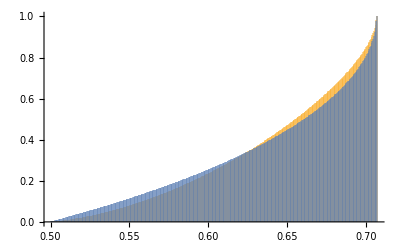

```mathematica
d=3;
r=ConstantArray[1.,4];
samplecount=1000000;
data1=CycleSample["Gyradius",d,r,samplecount,"QuotientSpace"->False];//AbsoluteTiming//First
data2=CycleSample["Gyradius",d,r,samplecount,"QuotientSpace"->True];//AbsoluteTiming//First
Histogram[{data1,data2},"Wand","CDF",PlotRange->All]
```

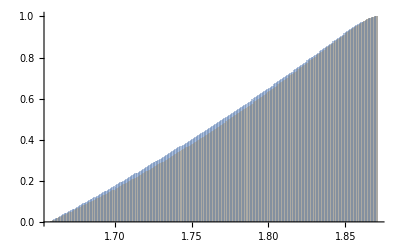

```mathematica
samplecount=1000000;
r={1,2,3,4};
ρ={1,1,3,3};
data1=CycleSample["Gyradius",d,r,samplecount,"QuotientSpace"->False,"SphereRadii"->r];
data2=CycleSample["Gyradius",d,r,samplecount,"QuotientSpace"->False,"SphereRadii"->ρ];
Histogram[{data1,data2},"Wand","CDF",PlotRange->All]
```

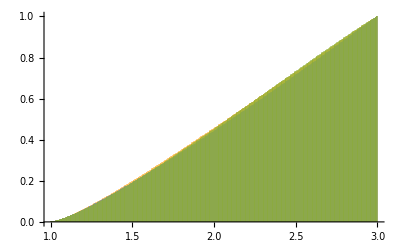

```mathematica
data1=CycleSampleChordLength[d,r,{1,3},samplecount,"QuotientSpace"->False,"SphereRadii"->r];
data2=CycleSampleChordLength[d,r,{1,3},samplecount,"QuotientSpace"->False,"SphereRadii"->Sqrt[r]];
data3=CycleSampleChordLength[d,r,{1,3},samplecount,"QuotientSpace"->False,"SphereRadii"->ρ];

Histogram[{data1,data2,data3},"Wand","CDF",PlotRange->All]
```

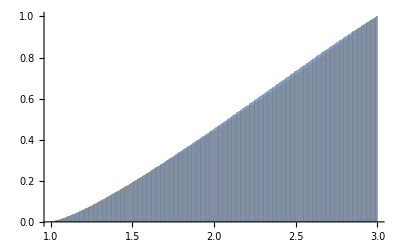

```mathematica
Histogram[{(*data1,*)data2,data3},"Wand","CDF",PlotRange->All]
```

0.119958

0.123702

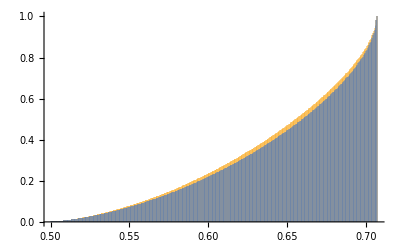

0.124969

0.12139

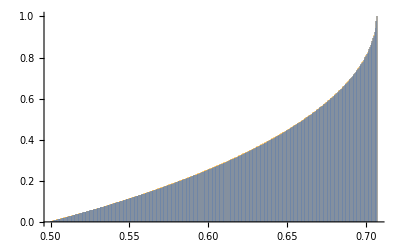

```mathematica
data1=CycleSample["Gyradius",d,r,samplecount,"QuotientSpace"->False];//AbsoluteTiming//First
data2=CycleSample["Gyradius",d,r,samplecount,"QuotientSpace"->False,"SphereRadii"->ρ];//AbsoluteTiming//First
Histogram[{data1,data2},"Wand","CDF",PlotRange->All]
```

```mathematica
"SphereRadii"
```

```mathematica
bla=RandomClosedPolygons[3,r,samplecount];
```

Compiling cRandomClosedPolygons[3]...

Reading build settings from /Users/Henrik/github/CycleSamplerLink/LibraryResources/Source/BuildSettings.m

Compilation done. Time elapsed = 2.10827 s.

A

B

C